#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatBrownAn00;
```

#### check that it’s symmetric, display info

```mathematica
MatrixNote[Tmat]
Tmat==Transpose[Tmat]
PrintVoigt[Tmat]
```

#### Set of Sigmas to use For the plotting, it’d be helpful to list these in order from TRIV (smallest beta) to ISO (largest beta).

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={ISO,CUBE,XISO,TRIG,TET,ORTH,MONO,TRIV};
```

```mathematica
ListSigma={MONO};
```

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};  (* default *)
```

#### Closest T to ISO

```mathematica
WantDetails="WantDetails";
```

```mathematica
MatrixNote[Tmat]
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

#### Choose Tmat1 (low symmetry) and Tmat2 (high symmetry)

```mathematica
MatrixNote[Tmat]
Tmat1 =Tmat ;
Tmat2 =TISO;
```

#### defaults for custom plotting (these will get overwritten below)

```mathematica
Sig1=TRIV;
Sig2=ISO;
ttop = 0.5;
```

#### Example: Brown TET triangle (supp1) TET to XISO segment for the Brown map Here TXISO is the closest to TRIV (Pathway 2), and β_XISO = 20.35^o

```mathematica
(* MatrixNote[Tmat]
Sig1=TET;
Sig2=XISO;
OutputFor[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TXISO=Closest[Tmat,Sig2];
Tmat1=TTET;
Tmat2=TXISO; 
ListSigma={TET,XISO}; 
ttop = 0.611707; *)
```

#### Example: Brown TET parabola (supp2) TET to CUBE segment for the Brown map Here TCUBE is the closest to TRIV (Pathway 2), and β_CUBE = 24.34^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TET;
Sig2=CUBE; 
OutputFor[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTET ;
Tmat2=TCUBE;
ListSigma={TET};*)
```

#### Example: Brown TRIG triangle (supp3) TRIG to CUBE segment for the Brown map Here CUBE is the closest to TRIV (Pathway 2), and β_CUBE = 21.12^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TRIG;
Sig2=CUBE; 
OutputFor[Tmat,Sig1]
TTRIG=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTRIG;
Tmat2=TCUBE;
ListSigma={TET,TRIG,MONO};
ttop=0.53515;*)
```

#### Example: Brown TET triangle (supp4) Experiment with different U to see if the triangle is sustained.

```mathematica
(*MatrixNote[Tmat]
OutputFor[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
(* UforNM1=UXISO.ZRot[25Degree]; *)
(* UforNM1=UXISO.XRot[1Degree].YRot[1Degree].ZRot[1Degree]; *)
Sig1=ORTH;
Sig2=TET;
TORTH=ProjToVSigOfU[Tmat,UforNM1,Sig1];
TTET=ProjToVSigOfU[Tmat,UforNM1,Sig2];
Tmat1=TORTH;
Tmat2=TTET; 
ListSigma={TET}; 
ttop=0.310400;*)
```

#### Example: Igel XISO inverted triangle (supp5) version 1: t1=0, t2=1, dt=0.05 version 2: t1=0.8, t2=0.9, dt=0.01

```mathematica
(*MatrixNote[Tmat]
OutputFor[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
Sig1=TET;
Sig2=CUBE;
TTET=ProjToVSigOfU[Tmat,UforNM1,Sig1];
TCUBE=ProjToVSigOfU[Tmat,UforNM1,Sig2];
Tmat1=TTET;
Tmat2=TCUBE; 
ListSigma={XISO}; 
ttop=0.8499757596500602;  (* solved in BC_XISObetweenTETandCUBE.nb *)
*)
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### check endpoints (but not that your chosen t values may exclude the endpoints)

```mathematica
MatrixNote[Tmat]
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

#### t values to use (note: you can choose to use t1 < 0 for the custom set of available maps)

```mathematica
Print["minimum allowable t is t1 = ",-tpert[Tmat] ];
```

```mathematica
(* Ranget=Join[{0},Range[t1,t2,dt],{1}] *)
```

```mathematica
t1 = 0.; t2 = 1.;dt=0.05; 
t1 = 0.8; t2 = 0.9;dt=0.01; 
Ranget=Range[t1,t2,dt];
```

#### Brown2016

```mathematica
t1 = -0.6;t2 = 1;dt=0.2; 
Ranget=Range[t1,t2,dt];
```

#### min and max values of t (these are used for plotting)

```mathematica
Ranget
tmin=Ranget[[1]]
tmax=Ranget[[Length[Ranget]]]
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
MatrixNote[Tmat]
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
OutputFor[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Optional: Plot the balls

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
```

```mathematica
contours[Tmat]
MaxForScaling[Tmat]
```

#### plot the 4th ball

```mathematica
If[False,Show[cpMONO[TT[Ranget[[4]],Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],options]]
```

#### plot all the balls (to plot an ISO ball, see BC_NodeMaps.nb)

```mathematica
If[False,Column[Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],options]&/@Ranget]]
```

## Calculate distance to each symmetry class KEY COMMAND: OutputFor performs the key calculations (minimizations)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
Ranget
```

```mathematica
ListSigma
```

```mathematica
(* OutputFor[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one OutputFor *)
```

```mathematica
Do[(Print["t = ",Ranget[[i]]];OutputFor[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]
```

## Optional: Plot the balls (this was motivated by the Brown TET triangle)

#### overwrite the default coloring for this Tmat (see chooseTmat.nb) cpMONO is in common_funs.nb; it requires defining the contours

```mathematica
(* Clear[contours,MaxForScaling]
contours[Tmat]=Range[0,20,2]
MaxForScaling[Tmat]=20 *)
```

#### function for plotting the U matrix (columns) For Sigma ≠ TRIV, Udots[Tmat, Sigma] should give the high symmetry axis (green) of a closest Sigma map to Tmat. For Sigma ≠ TRIV, MONO, Udots[Tmat, Sigma] should also give 2-fold axes (red, blue) of a closest Sigma map to Tmat.

```mathematica
Udots[Tmat_,Sigma_]:=Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.03],{ 
{Red,     Point[UT[Tmat, Sigma].{1,0,0}],Point[UT[Tmat, Sigma].{-1,0,0}]},
{Blue,   Point[UT[Tmat, Sigma].{0,1,0}],Point[UT[Tmat, Sigma].{0,-1,0}]},
{Green,Point[UT[Tmat, Sigma].{0,0,1}],Point[UT[Tmat, Sigma].{0,0,-1}]}}},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

#### main plot (Sig1 and Sig2 should be specified at the top)

```mathematica
(* Show[cpMONO[TT[Ranget[[2]],Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],options] *)
```

```mathematica
Nplot=0;
If[Length[Ranget] <Nplot,
{Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],options]&/@Ranget;
Udots[TT[#,Tmat1,Tmat2],Sig1]&/@Ranget;
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig1],  contours[Tmat],MaxForScaling[Tmat]],options]&/@Ranget; 
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig2],contours[Tmat],MaxForScaling[Tmat]],options]&/@Ranget}]
```

#### plot the U dots on a pair of plots for points on either side of the triangle (ttop should be specified at the top)

```mathematica
Ranget
```

```mathematica
Ranget1=Select[Ranget,#<=ttop&]    (* Note ≤ *)
Ranget2=Select[Ranget,#>ttop&]
```

```mathematica
ListMat1=TT[#,Tmat1,Tmat2]&/@Ranget1;
ListMat2=TT[#,Tmat1,Tmat2]&/@Ranget2;
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
MatrixForm[UT[#,Sig1]]&/@ListMat1
Print["Ranget2 = ",Ranget2];
MatrixForm[UT[#,Sig1]]&/@ListMat2
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat1},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
Print["Ranget2 = ",Ranget2];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat2},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

## Beta curves

```mathematica
ipick =Length[ListSigma];
ListSigma
Sigpick=ListSigma[[ipick]]
MatrixNote[Tmat]
Ranget
```

```mathematica
ColumnForm[{PaddedForm[#,{2,2}],Round[βT[TT[#,Tmat1,Tmat2],Sigpick]/Degree,.001]}&/@Ranget]
```

#### Angle in radians between Tmat and the closest-Sigma to Tmat is βT[Tmat, Sigma]

```mathematica
MatrixNote[Tmat]
βT[Tmat,Sigpick]
%/Degree
```

#### Plot all the beta curves together. This simple plot should always work

```mathematica
bcurve[Sigma_]:=Line[{#,βT[TT[#,Tmat1,Tmat2],Sigma]/Degree}&/@Ranget];
```

```mathematica
(* Ranget *)
```

```mathematica
(* bcurve/@ListSigma *)
```

```mathematica
MatrixNote[Tmat]
ListSigma
Graphics[bcurve/@ListSigma,Axes->True,AspectRatio->1,ImageSize->200]
```

#### Or pick only one from ListSigma (see ipick above)

```mathematica
bcurve[Sigpick]
Graphics[bcurve[Sigpick],Axes->True,AspectRatio->.8,ImageSize->200]
```

```mathematica
xran =Ranget[[Length[Ranget]]]-Ranget[[1]]
```

```mathematica
Max[Ranget]
```

```mathematica
Ranget
```

#### The fancier version has colored dots (hues are set in chooseTmat.nb)

```mathematica
PtOnβcurve[t_,Σ_]:={t,βT[TT[t,Tmat1,Tmat2],Σ]/Degree};
BetaCurve[Ranget_,Σ_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ],{n,1,Length[Ranget]}]};     
yvals=βT[TT[#,Tmat1,Tmat2],Last[ListSigma]]/Degree &/@ Ranget; (* based on the LAST Σ in the list *)
ymin=Min[yvals];
ymax=Max[yvals];
xmin=Min[Ranget];
xmax=Max[Ranget];
xran =xmax-xmin;
btextx=xmin-0.05xran; (* btextx=1.03tmax; *)
ylabelx=xmin-0.35xran; 
ylabely =0.5(ymin+ymax);
xlabelx=(Max[Ranget]+Min[Ranget])/2;
xlabely =-0.1ymax;
```

#### Drop TRIV from the list (and plot)

```mathematica
PSigma=ListSigma
(* PSigma=Drop[ListSigma,1] *)
```

```mathematica
Graphics[{PointSize[.02],
bcurve/@PSigma,
{HueOfΣ[#],BetaCurve[Ranget,#]}&/@PSigma,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmin,Tmat1,Tmat2],#]/Degree,0.01],")"],{HueOfΣ[#],15}], (* the text *)
                                                {btextx,βT[TT[tmin,Tmat1,Tmat2],#]/Degree},{1,0}]&/@PSigma,  (* the location of the text *)
Text[Style["β_Σ(t), degrees",22],{ylabelx,ylabely},{0,0},{0,1}], (* y-axis label *)
Text[Style["t",22],{xlabelx,xlabely},{0,0}] (* y-axis label *)
},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->600]
```

#### Pick one (your pick has to be from ListSigma)

```mathematica
Sig={TET};
```

```mathematica
Graphics[{PointSize[.02],
bcurve/@Sig,
{HueOfΣ[#],BetaCurve[Ranget,#]}&/@Sig,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmin,Tmat1,Tmat2],#]/Degree,0.01],")"],{HueOfΣ[#],12}],
                                                {btextx,βT[TT[tmin,Tmat1,Tmat2],#]/Degree},{1,0}]&/@Sig},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->300]
```

## For reference

#### Brown: t = –0.6 to t = 1, dt = 0.2, ListSigma = all

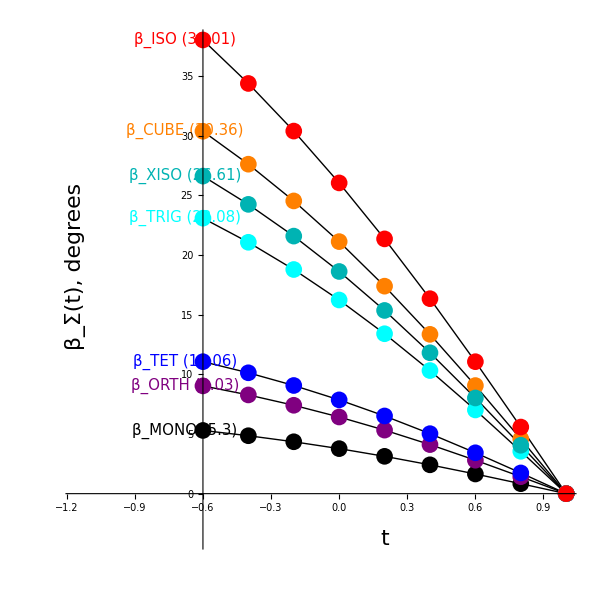

#### Brown: dt = 0.05, Tmat1=TTET, Tmat2=TXISO, ListSigma = {TET,XISO} [supp1]

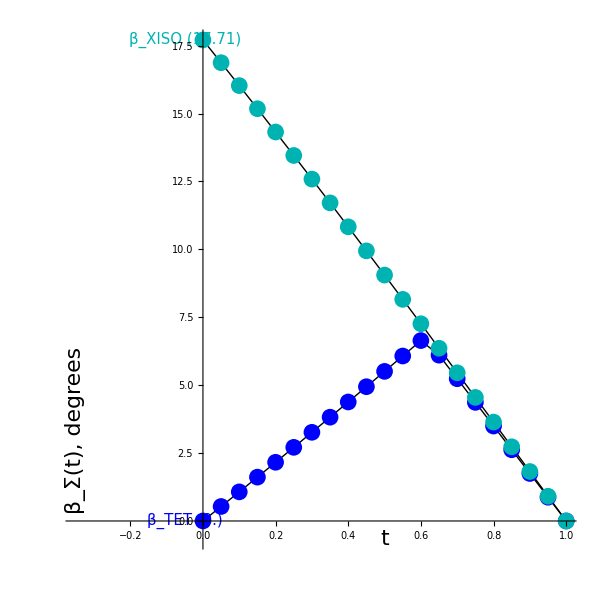

#### Brown: dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma={TET} [supp2]

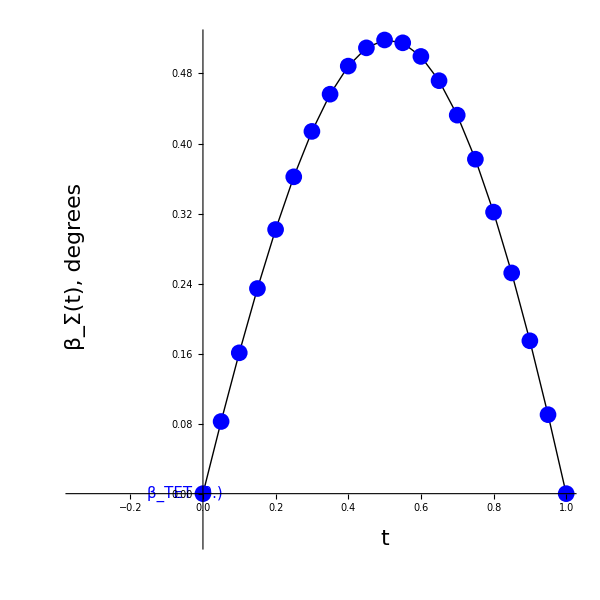

#### Brown: dt = 0.05, Tmat1=TTRIG, Tmat2=TCUBE, ListSigma={TET,TRIG,MONO} [supp3]

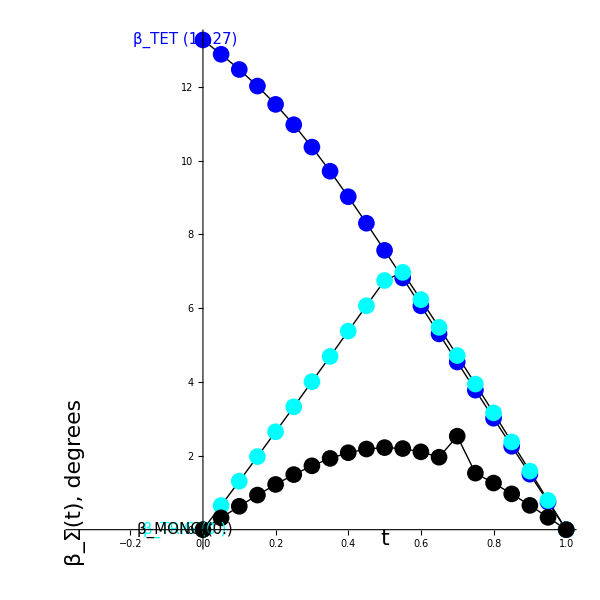

#### Brown dt = 0.05, Tmat1=TORTH, Tmat2=TTET, ListSigma = {TET}, nm1 with UforNM1 = UXISO [supp4]

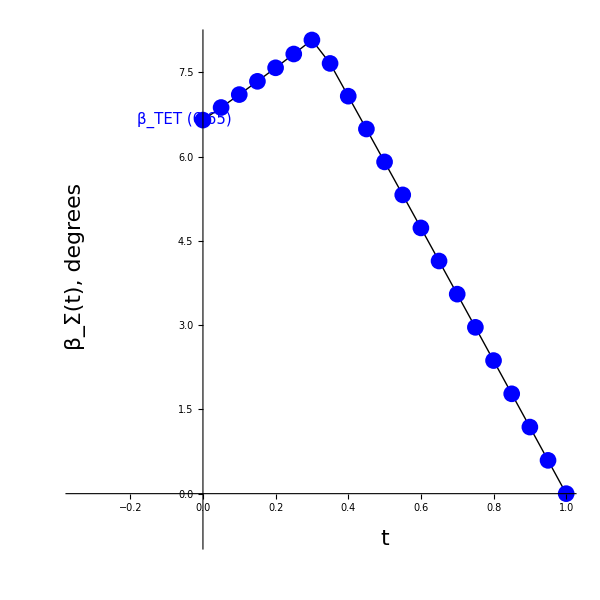

#### Igel dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma = {XISO}, nm1 with UforNM1 = UXISO [supp5]